# Numerical integration of λ^(n) (k=1, M=1)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nofpoints=200;
xmin=-20;
xmax=20;
```

```mathematica
prec=20;
```

```mathematica
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[x,{x,xmin,xmax,dx}];
f[x_,y_]:=dx*1/(2*π)*1/(2*Cosh[x/2])*(1/4*Tanh[x/2]*Tanh[y/2]-1/2*(Tanh[x/2]+Tanh[y/2])*(I*(x-y))/(4*π)+1/8-(x-y)^2/(32*π^2))*1/(4*Cosh[(x-y)/4]);
aA=Table[N[f[x,y],prec],{x,xlist},{y,xlist}];
(*v=e^(x/4)λ*)
v=Table[-1/(2*Cosh[x/2])*1/(√2)*Exp[x/4]*Exp[-(π*I)/8],{x,xlist}];
```

```mathematica
(*n=0*)
```

```mathematica
λ10210215=Import["../210215/k1_M1/210212_lambda_k1_s1_n0.m"];
```

```mathematica
λ10210215list=Table[(λ10210215/.{u->Exp[x/2],logu->x/2})*Exp[x/4],{x,xlist}];
```

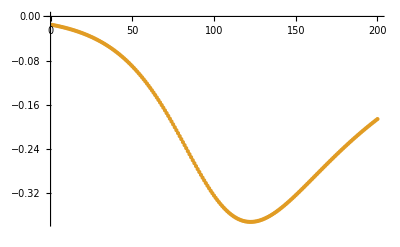

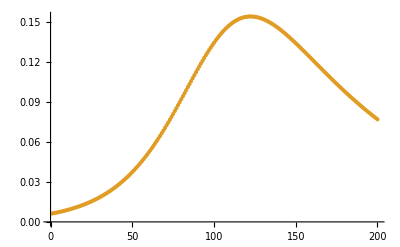

```mathematica
ListPlot[{Re[λ10210215list],Re[v]},Joined->{True,False}]
ListPlot[{Im[λ10210215list],Im[v]},Joined->{True,False}]
```

```mathematica
(*n=1*)
```

```mathematica
vnew=aA.v;
```

```mathematica
λ11210215=Import["../210215/k1_M1/210212_lambda_k1_s1_n1.m"];
```

```mathematica
λ11210215list=Table[(λ11210215/.{u->Exp[x/2],logu->x/2})*Exp[x/4],{x,xlist}];
```

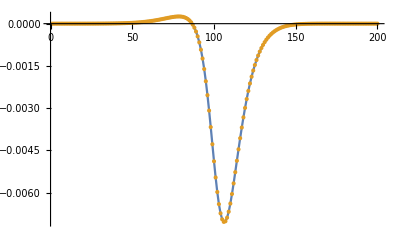

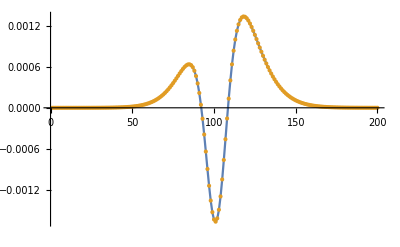

```mathematica
range=All;
ListPlot[{Re[λ11210215list],Re[vnew]},Joined->{True,False},PlotRange->range]
ListPlot[{Im[λ11210215list],Im[vnew]},Joined->{True,False},PlotRange->range]
```

```mathematica
(*n=2*)
```

```mathematica
vnew=aA.vnew;
```

```mathematica
λ12210215=Import["../210215/k1_M1/210212_lambda_k1_s1_n2.m"];
```

```mathematica
λ12210215list=Table[(λ12210215/.{u->Exp[x/2],logu->x/2})*Exp[x/4],{x,xlist}];
```

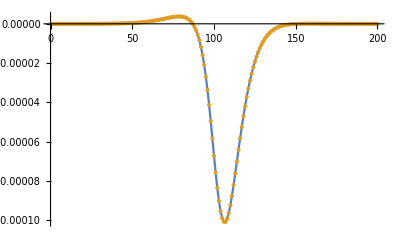

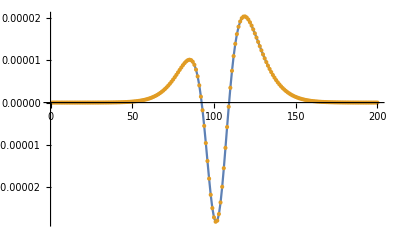

```mathematica
range=All;
ListPlot[{Re[λ12210215list],Re[vnew]},Joined->{True,False},PlotRange->range]
ListPlot[{Im[λ12210215list],Im[vnew]},Joined->{True,False},PlotRange->range]
```

# Numerical integration of λtilde^(n) (k=1, M=1)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nofpoints=200;
xmin=-20;
xmax=20;
```

```mathematica
prec=20;
```

```mathematica
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[x,{x,xmin,xmax,dx}];
f[x_,y_]:=dx*1/(2*π)*1/(2*Cosh[x/2])*(1/4*Tanh[x/2]*Tanh[y/2]+1/2*(Tanh[x/2]+Tanh[y/2])*(I*(x-y))/(4*π)+1/8-(x-y)^2/(32*π^2))*1/(4*Cosh[(x-y)/4]);
aAtilde=Table[N[f[x,y],prec],{x,xlist},{y,xlist}];
```

```mathematica
(*vtilde=e^(x/4)λtilde*)
vtilde=Table[-I/(2*√2)*Tanh[x/2]/(2*Cosh[x/2])*Exp[-x/4],{x,xlist}];
```

```mathematica
(*n=0*)
```

```mathematica
λtilde10210215=Import["../210215/k1_M1/210212_lambdatilde_k1_s1_n0.m"];
```

```mathematica
λtilde10210215list=Table[(λtilde10210215/.{u->Exp[x/2],logu->x/2})*Exp[x/4],{x,xlist}];
```

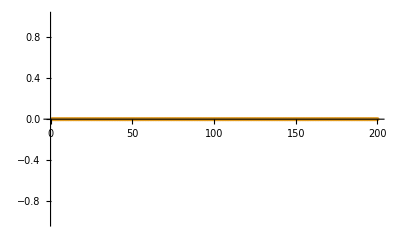

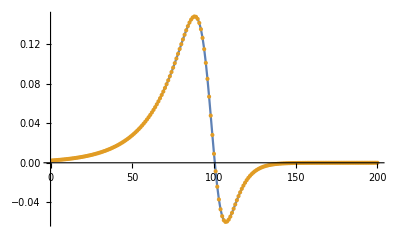

```mathematica
ListPlot[{Re[λtilde10210215list],Re[vtilde]},Joined->{True,False}]
ListPlot[{Im[λtilde10210215list],Im[vtilde]},Joined->{True,False}]
```

```mathematica
(*n=1*)
```

```mathematica
vtildenew=aAtilde.vtilde;
```

```mathematica
λ11tilde210215=Import["../210215/k1_M1/210212_lambdatilde_k1_s1_n1.m"];
```

```mathematica
λ11tilde210215list=Table[(λ11tilde210215/.{u->Exp[x/2],logu->x/2})*Exp[x/4],{x,xlist}];
```

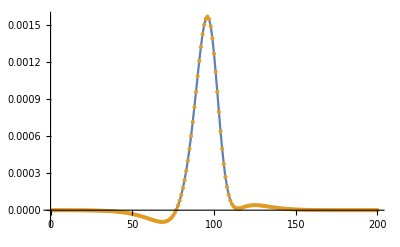

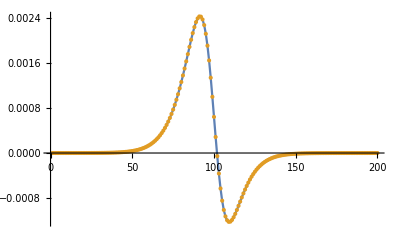

```mathematica
range=All;
ListPlot[{Re[λ11tilde210215list],Re[vtildenew]},Joined->{True,False},PlotRange->range]
ListPlot[{Im[λ11tilde210215list],Im[vtildenew]},Joined->{True,False},PlotRange->range]
```

```mathematica
(*n=2*)
```

```mathematica
vtildenew=aAtilde.vtildenew;
```

```mathematica
λ12tilde210215=Import["../210215/k1_M1/210212_lambdatilde_k1_s1_n2.m"];
```

```mathematica
λ12tilde210215list=Table[(λ12tilde210215/.{u->Exp[x/2],logu->x/2})*Exp[x/4],{x,xlist}];
```

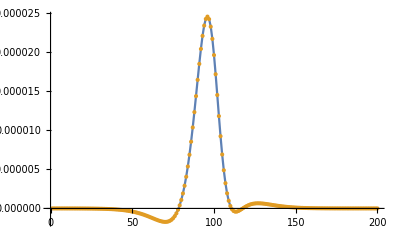

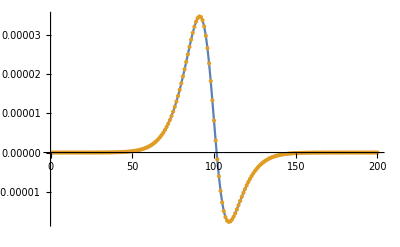

```mathematica
range=All;
ListPlot[{Re[λ12tilde210215list],Re[vtildenew]},Joined->{True,False},PlotRange->range]
ListPlot[{Im[λ12tilde210215list],Im[vtildenew]},Joined->{True,False},PlotRange->range]
```

```mathematica
(*n=3*)
```

```mathematica
vtildenew=aAtilde.vtildenew;
```

```mathematica
λ12tilde210215=Import["../210215/k1_M1/210212_lambdatilde_k1_s1_n3.m"];
```

```mathematica
λ12tilde210215list=Table[N[(λ12tilde210215/.{u->Exp[x/2],logu->x/2})*Exp[x/4],prec],{x,xlist}];
```

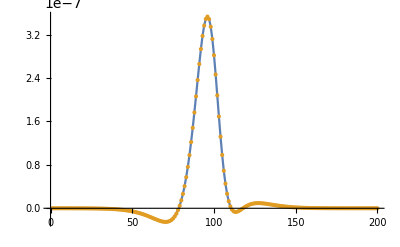

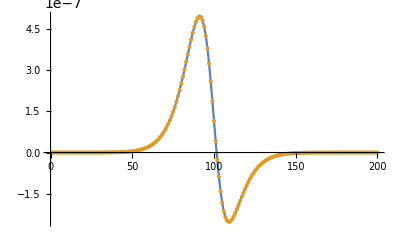

```mathematica
range=All;
ListPlot[{Re[λ12tilde210215list],Re[vtildenew]},Joined->{True,False},PlotRange->range]
ListPlot[{Im[λ12tilde210215list],Im[vtildenew]},Joined->{True,False},PlotRange->range]
```

# Numerical integration of (H_12’ )_(11,n) and ( H_13 )_(11,n) (k=1, M=1)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nofpoints=200;
xmin=-20;
xmax=20;
```

```mathematica
prec=20;
```

```mathematica
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[x,{x,xmin,xmax,dx}];
f[x_,y_]:=(Exp[-x/2]+1)*dx*1/(2*π)*1/(2*Cosh[x/2])*(1/4*Tanh[x/2]*Tanh[y/2]-1/2*(Tanh[x/2]+Tanh[y/2])*(I*(x-y))/(4*π)+1/8-(x-y)^2/(32*π^2))*1/(4*Cosh[(x-y)/4])*1/(Exp[-y/2]+1);
aA=Table[N[f[x,y],prec],{x,xlist},{y,xlist}];
(*v=(e^(-x/2)+1)e^(x/4)λ*)
c12=Table[N[-Exp[(π*I)/8]*1/(√2)*dx/(2*π)*Exp[-x/4]*(I*Tanh[x/2])/2*1/(Exp[-x/2]+1),prec],{x,xlist}];
c13=Table[N[dx*1/(2*π*√2)*Exp[(π*I)/8]*Exp[-x/4]*1/(Exp[-x/2]+1),prec],{x,xlist}];
v=Table[(Exp[-x/2]+1)*(-1/(2*Cosh[x/2])*1/(√2)*Exp[x/4]*Exp[-(π*I)/8]),{x,xlist}];
```

```mathematica
(*n=0*)
```

```mathematica
H12prime0=c12.v;
H130=c13.v;
```

```mathematica
H12prime0210215=Import["../210215/k1_M1/210212_H12primesrn_k1_r1_s1_n0.m"];
H130210215=Import["../210215/k1_M1/210212_H13srn_k1_r1_s1_n0.m"];
```

```mathematica
H12prime0
N[H12prime0210215,3]
(**)
H130
N[H130210215,3]
```

0.+0. ⅈ

0

-0.24998626278482884408+0. ⅈ

-0.25+0. ⅈ

```mathematica
(*n=1*)
```

```mathematica
vnew=aA.v;
```

```mathematica
H12prime1=c12.vnew;
H131=c13.vnew;
```

```mathematica
H12prime1210215=Import["../210215/k1_M1/210212_H12primesrn_k1_r1_s1_n1.m"];
H131210215=Import["../210215/k1_M1/210212_H13srn_k1_r1_s1_n1.m"];
```

```mathematica
H12prime1
N[H12prime1210215,3]
(**)
H131
N[H131210215,3]
```

-0.000566536464019527545+0.0005261086397425355439 ⅈ

-0.000568+0.00053 ⅈ

-0.001958158227616440001+0. ⅈ

-0.00195+0. ⅈ

```mathematica
(*n=2*)
```

```mathematica
vnew=aA.vnew;
```

```mathematica
H12prime2=c12.vnew;
H132=c13.vnew;
```

```mathematica
H12prime2210215=Import["../210215/k1_M1/210212_H12primesrn_k1_r1_s1_n2.m"];
H132210215=Import["../210215/k1_M1/210212_H13srn_k1_r1_s1_n2.m"];
```

```mathematica
H12prime2
N[H12prime2210215,3]
(**)
H132
N[H132210215,3]
```

-8.44218115825324998×10^-6+7.50625975220298577×10^-6 ⅈ

-8.45×10^-6+7.5×10^-6 ⅈ

-0.0000269754807504424087+0. ⅈ

-0.0000269+0. ⅈ

```mathematica
(*n=3*)
```

```mathematica
vnew=aA.vnew;
```

```mathematica
H12prime3=c12.vnew;
H133=c13.vnew;
```

```mathematica
H12prime3210215=Import["../210215/k1_M1/210212_H12primesrn_k1_r1_s1_n3.m"];
H133210215=Import["../210215/k1_M1/210212_H13srn_k1_r1_s1_n3.m"];
```

```mathematica
H12prime3
N[H12prime3210215,3]
(**)
H133
N[H133210215,3]
```

-1.20762805116624536×10^-7+1.07015213430200581×10^-7 ⅈ

-1.21×10^-7+1.1×10^-7 ⅈ

-3.83682346925777277×10^-7+0. ⅈ

-3.83×10^-7+0. ⅈ

# Numerical integration of (H_14’ )_(11,n) (k=1, M=1)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nofpoints=200;
xmin=-20;
xmax=20;
```

```mathematica
prec=20;
```

```mathematica
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[x,{x,xmin,xmax,dx}];
f[x_,y_]:=dx*1/(2*π)*1/(2*Cosh[x/2])*(1/4*Tanh[x/2]*Tanh[y/2]-1/2*(Tanh[x/2]+Tanh[y/2])*(I*(x-y))/(4*π)+1/8-(x-y)^2/(32*π^2))*1/(4*Cosh[(x-y)/4]);
aA=Table[N[f[x,y],prec],{x,xlist},{y,xlist}];
(*v=e^(x/4)λ*)
y0=π*I;
c14=Table[N[1/(√I)*Exp[-(π*I)/8]*dx/(2*π)*(Tanh[x/2]/2*(I*(y0-x))/(4*π)-(1/8-(y0-x)^2/(32*π^2)))*1/(4*Cosh[(y0-x)/4]),prec],{x,xlist}];
v=Table[-1/(2*Cosh[x/2])*1/(√2)*Exp[x/4]*Exp[-(π*I)/8],{x,xlist}];
```

```mathematica
(*n=0*)
```

```mathematica
H14prime0=c14.v;
```

```mathematica
H14prime0210215=Import["../210215/k1_M1/210212_H14primesrn_k1_r1_s1_n0.m"];
```

```mathematica
H14prime0
N[H14prime0210215,3]
```

0.01495961646959174173-0.01165294942681071149 ⅈ

0.015-0.012 ⅈ

```mathematica
(*n=1*)
```

```mathematica
vnew=aA.v;
```

```mathematica
H14prime1=c14.vnew;
```

```mathematica
H14prime1210215=Import["../210215/k1_M1/210212_H14primesrn_k1_r1_s1_n1.m"];
```

```mathematica
H14prime1
N[H14prime1210215,3]
```

0.0002662167648793469175-0.0001538144678231943704 ⅈ

0.000266-0.00015 ⅈ

```mathematica
(*n=2*)
```

```mathematica
vnew=aA.vnew;
```

```mathematica
H14prime2=c14.vnew;
```

```mathematica
H14prime2210215=Import["../210215/k1_M1/210212_H14primesrn_k1_r1_s1_n2.m"];
```

```mathematica
H14prime2
N[H14prime2210215,3]
```

3.857151134554585703×10^-6-2.15867525700308768×10^-6 ⅈ

3.86×10^-6-2.2×10^-6 ⅈ

```mathematica
(*n=3*)
```

```mathematica
vnew=aA.vnew;
```

```mathematica
H14prime3=c14.vnew;
```

```mathematica
H14prime3210215=Import["../210215/k1_M1/210212_H14primesrn_k1_r1_s1_n3.m"];
```

```mathematica
H14prime3
N[H14prime3210215,3]
```

5.507431930843863004×10^-8-3.07410873733935221×10^-8 ⅈ

5.51×10^-8-3.1×10^-8 ⅈ

# Numerical integration of ( H_24 ‘’ )_(11,n) (k=1, M=1)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nofpoints=200;
xmin=-20;
xmax=20;
```

```mathematica
prec=20;
```

```mathematica
dx=(xmax-xmin)/(nofpoints-1);
xlist=Table[x,{x,xmin,xmax,dx}];
f[x_,y_]:=(Exp[x/2]+1)*dx*1/(2*π)*1/(2*Cosh[x/2])*(1/4*Tanh[x/2]*Tanh[y/2]+1/2*(Tanh[x/2]+Tanh[y/2])*(I*(x-y))/(4*π)+1/8-(x-y)^2/(32*π^2))*1/(4*Cosh[(x-y)/4])*1/(Exp[y/2]+1);
aAtilde=Table[N[f[x,y],prec],{x,xlist},{y,xlist}];
```

```mathematica
c24=Table[N[I/(4*π*√2)*Tanh[x/2]*Exp[x/4]*1/(Exp[x/2]+1)*dx,prec],{x,xlist}];
(*vtilde=(e^(x/2)+1)e^(x/4)λtilde*)
vtilde=Table[(Exp[x/2]+1)*(-I/(2*√2)*Tanh[x/2]/(2*Cosh[x/2])*Exp[-x/4]),{x,xlist}];
```

```mathematica
(*n=0*)
```

```mathematica
H24primeprime0=c24.vtilde;
H24primeprime0210215=Import["../210215/k1_M1/210212_H24primeprimesrn_k1_r1_s1_n0.m"];
```

```mathematica
H24primeprime0
N[H24primeprime0210215,3]
```

0.031246565696215718072

0.0313

```mathematica
(*n=1*)
```

```mathematica
vtildenew=aAtilde.vtilde;
```

```mathematica
H24primeprime1=c24.vtildenew;
H24primeprime1210215=Import["../210215/k1_M1/210212_H24primeprimesrn_k1_r1_s1_n1.m"];
```

```mathematica
H24primeprime1
N[H24primeprime1210215,3]
```

0.0006858266047005671447+0. ⅈ

0.000686+0. ⅈ

```mathematica
(*n=2*)
```

```mathematica
vtildenew=aAtilde.vtildenew;
```

```mathematica
H24primeprime2=c24.vtildenew;
H24primeprime2210215=Import["../210215/k1_M1/210212_H24primeprimesrn_k1_r1_s1_n2.m"];
```

```mathematica
H24primeprime2
N[H24primeprime2210215,3]
```

9.633521836630543276×10^-6+0. ⅈ

9.63×10^-6+0. ⅈ

```mathematica
(*n=3*)
```

```mathematica
vtildenew=aAtilde.vtildenew;
```

```mathematica
H24primeprime3=c24.vtildenew;
H24primeprime3210215=Import["../210215/k1_M1/210212_H24primeprimesrn_k1_r1_s1_n3.m"];
```

```mathematica
H24primeprime3
N[H24primeprime3210215,3]
```

1.371936358817879261×10^-7+0. ⅈ

1.37×10^-7+0. ⅈ

# Direct evaluation of eq(5.8) (6 dimensional integral)

```mathematica
Quit[];
```

```mathematica
k1=1-I*ϵ;
k2=1+I*ϵ;
```

```mathematica
ϵ=0.01;
```

```mathematica
nofpoints=200;
xmin=-20;
xmax=20;
prec=20;
dx=(xmax-xmin)/(nofpoints-1);
```

```mathematica
xmin=-100;
xmax=100;
```

```mathematica
ξlist=Table[i,{i,xmin,xmax,dx}];
ξprimelist=Table[i+dx/2,{i,xmin,xmax,dx}];
```

```mathematica
mat1={{1/(2*Sinh[(ξ-ξprime1)/2]),1/(2*Sinh[(ξ-ξprime2)/2])},
{Exp[1/2*ξprime1],Exp[1/2*ξprime2]}};
(**)

mat2={{lL[ξ,η],lL[ξ,ηprime1],lL[ξ,ηprime2],exp[1/2*ξ]},
{lL[ξprime1,η],lL[ξprime1,ηprime1],lL[ξprime1,ηprime2],exp[1/2*ξprime1]},
{lL[ξprime2,η],lL[ξprime2,ηprime1],lL[ξprime2,ηprime2],exp[1/2*ξprime2]},
{exp[-1/2*η],exp[-1/2*ηprime1],exp[-1/2*ηprime2],0}};
(*
mat2={{lL[ξ,η],lL[ξ,ηprime1],lL[ξ,ηprime2],Exp[1/2*ξ]},
{lL[ξprime1,η],lL[ξprime1,ηprime1],lL[ξprime1,ηprime2],Exp[1/2*ξprime1]},
{lL[ξprime2,η],lL[ξprime2,ηprime1],lL[ξprime2,ηprime2],Exp[1/2*ξprime2]},
{Exp[-1/2*η],Exp[-1/2*ηprime1],Exp[-1/2*ηprime2],0}};
*)
(**)

mat3={{1/(2*Sinh[(η-ηprime1)/2]),1/(2*Sinh[(η-ηprime2)/2])},
{Exp[-1/2*ηprime1],Exp[-1/2*ηprime2]}};

(**)
(2!)^2*-1/(2!)^2(1/(2*π))^6
Exp[-(I*k1)/(2*π)*ξprime1^2-ξprime1]
Exp[-(I*k1)/(2*π)*ξprime2^2-1/2*ξprime2]
Exp[(I*k2)/(2*π)*ηprime1^2+ηprime1]
Exp[(I*k2)/(2*π)*ηprime2^2+1/2*ηprime2]
1/(2*Sinh[(ξ-ξprime1)/2])
1/(2*Sinh[(η-ηprime1)/2])
```

-1/(64 π^6)

ⅇ^(-ξprime1-(ⅈ k1 ξprime1^2)/(2 π))

ⅇ^(-ξprime2/2-(ⅈ k1 ξprime2^2)/(2 π))

ⅇ^(ηprime1+(ⅈ k2 ηprime1^2)/(2 π))

ⅇ^(ηprime2/2+(ⅈ k2 ηprime2^2)/(2 π))

1/2 Csch[(ξ-ξprime1)/2]

1/2 Csch[(η-ηprime1)/2]

```mathematica
Det[mat1]Det[mat2]Det[mat3]//Expand//Cancel
```

```mathematica
exp[x_]:=Exp[x];
lL[x_,y_]:=1/(2*Cosh[(x-y)/2]);
```

```mathematica
one[[1]]
```

```mathematica
ans11=dx*Total[N[Table[exp[-ηprime2/2]*Exp[(I*k2)/(2*π)*ηprime2^2+1/2*ηprime2],{ηprime2,ξprimelist}],prec]];
(**)
ans12=dx*Total[N[Table[exp[ξprime2/2]*Exp[-(I*k1)/(2*π)*ξprime2^2-1/2*ξprime2],{ξprime2,ξprimelist}],prec]];
(**)
ans13=dx^4*Total[N[Flatten[Table[lL[ξ,ηprime1]*lL[ξprime1,η]*Exp[-(I*k1)/(2*π)*ξprime1^2-ξprime1]*1/(2*Sinh[(ξ-ξprime1)/2])*Exp[(I*k2)/(2*π)*ηprime1^2+ηprime1]*1/(2*Sinh[(η-ηprime1)/2]),{ξ,ξlist},{η,ξlist},{ξprime1,ξprimelist},{ηprime1,ξprimelist}]],prec]];
ans1=ans11*ans12*ans13;
(**)
```

$Aborted

```mathematica
ϵ2=1.*10^-4;
Print[DateString[]];
ans13NI=NIntegrate[lL[ξ,ηprime1]*lL[ξprime1,η]*Exp[-(I*k1)/(2*π)*ξprime1^2-ξprime1]*1/(2*Sinh[(ξ-ξprime1)/2])*Exp[(I*k2)/(2*π)*ηprime1^2+ηprime1]*1/(2*Sinh[(η-ηprime1)/2]),{ξ,xmin,xmax},{η,xmin,xmax},{ξprime1,xmin,xmax},{ηprime1,xmin,xmax}];
(*
ans13NI=NIntegrate[lL[ξ,ηprime1]*lL[ξprime1,η]*Exp[-(I*k1)/(2*π)*ξprime1^2-ξprime1]*1/(2*Sinh[(ξ-ξprime1)/2+I*ϵ2])*Exp[(I*k2)/(2*π)*ηprime1^2+ηprime1]*1/(2*Sinh[(η-ηprime1)/2+I*ϵ2]),{ξ,xmin,xmax},{η,xmin,xmax},{ξprime1,xmin,xmax},{ηprime1,xmin,xmax}];
*)
Print[DateString[]];
```

Tue 16 Feb 2021 18:31:21

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 36 recursive bisections in ηprime1 near {ξ,η,ξprime1,ηprime1} = {-1.94845,68.8247,-6.73711,-7.08844×10^-12}. NIntegrate obtained 1.64962×10^39-9.34774×10^39 ⅈ and 3.45448×10^39 for the integral and error estimates.

Tue 16 Feb 2021 18:39:18

```mathematica
ans13NI
```

1.64962×10^39-9.34774×10^39 ⅈ

```mathematica
one=Det[mat2];
```

```mathematica
onelist=List@@(one//Expand)
```

{exp[-ηprime2/2] exp[ξprime2/2] lL[ξ,ηprime1] lL[ξprime1,η],-exp[-ηprime1/2] exp[ξprime2/2] lL[ξ,ηprime2] lL[ξprime1,η],-exp[-ηprime2/2] exp[ξprime2/2] lL[ξ,η] lL[ξprime1,ηprime1],exp[-η/2] exp[ξprime2/2] lL[ξ,ηprime2] lL[ξprime1,ηprime1],exp[-ηprime1/2] exp[ξprime2/2] lL[ξ,η] lL[ξprime1,ηprime2],-exp[-η/2] exp[ξprime2/2] lL[ξ,ηprime1] lL[ξprime1,ηprime2],-exp[-ηprime2/2] exp[ξprime1/2] lL[ξ,ηprime1] lL[ξprime2,η],exp[-ηprime1/2] exp[ξprime1/2] lL[ξ,ηprime2] lL[ξprime2,η],exp[-ηprime2/2] exp[ξ/2] lL[ξprime1,ηprime1] lL[ξprime2,η],-exp[-ηprime1/2] exp[ξ/2] lL[ξprime1,ηprime2] lL[ξprime2,η],exp[-ηprime2/2] exp[ξprime1/2] lL[ξ,η] lL[ξprime2,ηprime1],-exp[-η/2] exp[ξprime1/2] lL[ξ,ηprime2] lL[ξprime2,ηprime1],-exp[-ηprime2/2] exp[ξ/2] lL[ξprime1,η] lL[ξprime2,ηprime1],exp[-η/2] exp[ξ/2] lL[ξprime1,ηprime2] lL[ξprime2,ηprime1],-exp[-ηprime1/2] exp[ξprime1/2] lL[ξ,η] lL[ξprime2,ηprime2],exp[-η/2] exp[ξprime1/2] lL[ξ,ηprime1] lL[ξprime2,ηprime2],exp[-ηprime1/2] exp[ξ/2] lL[ξprime1,η] lL[ξprime2,ηprime2],-exp[-η/2] exp[ξ/2] lL[ξprime1,ηprime1] lL[ξprime2,ηprime2]}

```mathematica
Length[%]
```

18

```mathematica
onelist[[1]]
```

exp[-ηprime2/2] exp[ξprime2/2] lL[ξ,ηprime1] lL[ξprime1,η]

```mathematica
onelist[[18]]
```

```mathematica
-exp[-η/2] exp[ξ/2] lL[ξprime1,ηprime1] lL[ξprime2,ηprime2]Csch[(η-ηprime2)/2] Csch[(ξ-ξprime2)/2]Csch[(η-ηprime1)/2] Csch[(ξ-ξprime1)/2]
```

```mathematica
Integrate[Exp[-ξ/2]/(2Sinh[(ξ-ξ1)/2]2Sinh[(ξ-ξ2)/2]),{ξ,-Infinity,Infinity},PrincipalValue->True]
```

$Aborted

```mathematica
-1/4 ⅇ^(-η/2-ηprime1/2+ξ/2+ξprime1/2) Csch[(η-ηprime2)/2] Csch[(ξ-ξprime2)/2] lL[ξprime1,ηprime1] lL[ξprime2,ηprime2]
```

```mathematica
Integrate[,{η,ηprime2,ξprime2,ξ}]*Integrate[,{ξprime1,ηprime1}]
```

```mathematica
(ξprime[i],ηprime[j],ξ,η),(ξprime[3-i],ηprime[3-j])
```

# Residue of higher pole calculated by hand [13:26, 16 Feb 2021]

## k=1, M=1, N=1, (λ^(1))_1 (ok)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    rewrite residues of double pole (require derivatives) by hand into simple substitutions*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
λ00v=-1/(√2)*Exp[-(π*I)/8]*v/(v^2+1);
(**)
λ1byhandresidue1=1/(2*π)*u/(u^2+1)*λ00v*(-(2*π*I)*BernoulliB[1,(logu+π*I)/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)*(v^2-1)/(v^2+1)-I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))*logu+1/8-1/(8*π^2)*logu^2)-(2*π*I)^2/2*BernoulliB[2,(logu+π*I)/(2*π*I)]*(I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))+1/(4*π^2)*logu)-(2*π*I)^3/3*BernoulliB[3,(logu+π*I)/(2*π*I)]*(-1/(8*π^2)))/.{v->-u}//FullSimplify;
(**)
λ1byhandresidue21=1/(2*π)*u/(u^2+1)*(-1/(√2)*Exp[-(π*I)/8]*v/(v+I)*1/(v+u)*(-(2*π*I)*BernoulliB[1,((π*I)/2)/(2*π*I)]*(-I/(4*π)*(u^2-1)/(u^2+1)*logu+1/8-1/(8*π^2)*logu^2)-(2*π*I)^2/2*BernoulliB[2,((π*I)/2)/(2*π*I)]*(I/(4*π)*(u^2-1)/(u^2+1)+1/(4*π^2)*logu)-(2*π*I)^3/3*BernoulliB[3,((π*I)/2)/(2*π*I)]*(-1/(8*π^2)))/.{v->I})//FullSimplify;
(**)
λ1byhandresidue22=1/(2*π)*u/(u^2+1)*(-1/(√2)*Exp[-(π*I)/8]*v/(v-I)*1/(v+u)*(-(2*π*I)*BernoulliB[1,((3*π*I)/2)/(2*π*I)]*(-I/(4*π)*(u^2-1)/(u^2+1)*logu+1/8-1/(8*π^2)*logu^2)-(2*π*I)^2/2*BernoulliB[2,((3*π*I)/2)/(2*π*I)]*(I/(4*π)*(u^2-1)/(u^2+1)+1/(4*π^2)*logu)-(2*π*I)^3/3*BernoulliB[3,((3*π*I)/2)/(2*π*I)]*(-1/(8*π^2)))/.{v->-I})//FullSimplify;
(**)
λ1byhandresidue31=1/(2*π)*u/(u^2+1)*(-1/(√2)*Exp[-(π*I)/8]*(((v^2-1)/((v+I)^2*(v+u))+(2*v^2)/((v+I)^2*(v+u))-(2*v*(v^2-1))/((v+I)^3*(v+u))-(v*(v^2-1))/((v+I)^2*(v+u)^2))*(-2*π*I*BernoulliB[1,((π*I)/2)/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)-I/(4*π)*logu)-(2*π*I)^2/2*BernoulliB[2,((π*I)/2)/(2*π*I)]*(I/(4*π)))+(v*(v^2-1))/((v+I)^2*(v+u))*1/(2*π*I*v)*(-2*π*I*BernoulliB[0,((π*I)/2)/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)-I/(4*π)*logu)-(2*π*I)^2*BernoulliB[1,((π*I)/2)/(2*π*I)]*(I/(4*π))))/.{v->I})//FullSimplify;
(**)
λ1byhandresidue32=1/(2*π)*u/(u^2+1)*(-1/(√2)*Exp[-(π*I)/8]*(((v^2-1)/((v-I)^2*(v+u))+(2*v^2)/((v-I)^2*(v+u))-(2*v*(v^2-1))/((v-I)^3*(v+u))-(v*(v^2-1))/((v-I)^2*(v+u)^2))*(-2*π*I*BernoulliB[1,((3*π*I)/2)/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)-I/(4*π)*logu)-(2*π*I)^2/2*BernoulliB[2,((3*π*I)/2)/(2*π*I)]*(I/(4*π)))+(v*(v^2-1))/((v-I)^2*(v+u))*1/(2*π*I*v)*(-2*π*I*BernoulliB[0,((3*π*I)/2)/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)-I/(4*π)*logu)-(2*π*I)^2*BernoulliB[1,((3*π*I)/2)/(2*π*I)]*(I/(4*π))))/.{v->-I})//FullSimplify;
(**)
λ1byhand=λ1byhandresidue1+λ1byhandresidue21+λ1byhandresidue22+λ1byhandresidue31+λ1byhandresidue32;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Mathematica code on 210215*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
λ1210215=Import["../210215/k1_M1/210212_lambda_k1_s1_n1.m"]//FullSimplify;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Mathematica code on 210215, substitute k=1,M=1,r=1,s=1,j=0 explicitly*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
λold=-1/(√2)*Exp[-(π*I)/8]*v/(v^2+1);
```

```mathematica
λ1residue1=1/(2*π)*u/(u^2+1)*Residue[(λold/(u+v)*(-(2*π*I)*BernoulliB[1,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)*(v^2-1)/(v^2+1)-I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))*logu+1/8-1/(8*π^2)*logu^2)-(2*π*I)^2/2*BernoulliB[2,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]*(I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))+1/(4*π^2)*logu)-(2*π*I)^3/3*BernoulliB[3,(logu+π*I+Log[1-u^-1*dv])/(2*π*I)]*(-1/(8*π^2)))/.{v->-u+dv}),{dv,0}]//FullSimplify;
λ1residue2=1/(2*π)*u/(u^2+1)*Residue[(λold/(u+v)*(-(2*π*I)*BernoulliB[1,((π*I)/2+Log[1-I*dv])/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)*(v^2-1)/(v^2+1)-I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))*logu+1/8-1/(8*π^2)*logu^2)-(2*π*I)^2/2*BernoulliB[2,((π*I)/2+Log[1-I*dv])/(2*π*I)]*(I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))+1/(4*π^2)*logu)-(2*π*I)^3/3*BernoulliB[3,((π*I)/2+Log[1-I*dv])/(2*π*I)]*(-1/(8*π^2)))/.{v->I+dv}),{dv,0}]//FullSimplify;
λ1residue3=1/(2*π)*u/(u^2+1)*Residue[(λold/(u+v)*(-(2*π*I)*BernoulliB[1,((3*π*I)/2+Log[1+I*dv])/(2*π*I)]*(1/4*(u^2-1)/(u^2+1)*(v^2-1)/(v^2+1)-I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))*logu+1/8-1/(8*π^2)*logu^2)-(2*π*I)^2/2*BernoulliB[2,((3*π*I)/2+Log[1+I*dv])/(2*π*I)]*(I/(4*π)*((u^2-1)/(u^2+1)+(v^2-1)/(v^2+1))+1/(4*π^2)*logu)-(2*π*I)^3/3*BernoulliB[3,((3*π*I)/2+Log[1+I*dv])/(2*π*I)]*(-1/(8*π^2)))/.{v->-I+dv}),{dv,0}]//FullSimplify;
λ1=λ1residue1+λ1residue2+λ1residue3;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Compare*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
λ1byhand-λ1210215//FullSimplify
```

0

```mathematica
λ1byhand-λ1//FullSimplify
```

0

## k=1, M=1, N=1, (H'_12 )_(11,0) (ok)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    rewrite residues of double pole (require derivatives) by hand into simple substitutions*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
H12prime110byhandresidue1=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*(-1/(√2)*Exp[-(π*I)/8])*(((2*u)/(u+I)^2-(2*(u^2-1))/(u+I)^3)*BernoulliB[1,((π*I)/2)/(2*π*I)]+(u^2-1)/(u+I)^2*1/(2*π*I*u)*BernoulliB[0,((π*I)/2)/(2*π*I)])/.{u->I}//FullSimplify;
H12prime110byhandresidue2=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*(-1/(√2)*Exp[-(π*I)/8])*(((2*u)/(u-I)^2-(2*(u^2-1))/(u-I)^3)*BernoulliB[1,((3*π*I)/2)/(2*π*I)]+(u^2-1)/(u-I)^2*1/(2*π*I*u)*BernoulliB[0,((3*π*I)/2)/(2*π*I)])/.{u->-I}//FullSimplify;
H12prime110byhand=H12prime110byhandresidue1+H12prime110byhandresidue2;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Mathematica code on 210215*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
H12prime110210215=Import["../210215/k1_M1/210212_H12primesrn_k1_r1_s1_n0.m"]//FullSimplify;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Mathematica code on 210215, substitute k=1,M=1,r=1,s=1,j=0 explicitly*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
λ00=-1/(√2)*Exp[-(π*I)/8]*u/(u^2+1);
(**)
H12prime110residue1=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*Residue[(u^-1*(u^2-1)/(u^2+1)*λ00*BernoulliB[1,((π*I)/2+Log[1-I*du])/(2*π*I)]/.{u->I+du}),{du,0}];
H12prime110residue2=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*Residue[(u^-1*(u^2-1)/(u^2+1)*λ00*BernoulliB[1,((3*π*I)/2+Log[1+I*du])/(2*π*I)]/.{u->-I+du}),{du,0}];
H12prime110=H12prime110residue1+H12prime110residue2;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Compare*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
H12prime110byhand-H12prime110210215//FullSimplify
```

0

```mathematica
H12prime110byhand-H12prime110//FullSimplify
```

0

## k=1, M=1, N=1, (H_13 )_(11,0)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    rewrite residues of double pole (require derivatives) by hand into simple substitutions*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
H12prime110byhandresidue1=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*(-1/(√2)*Exp[-(π*I)/8])*(((2*u)/(u+I)^2-(2*(u^2-1))/(u+I)^3)*BernoulliB[1,((π*I)/2)/(2*π*I)]+(u^2-1)/(u+I)^2*1/(2*π*I*u)*BernoulliB[0,((π*I)/2)/(2*π*I)])/.{u->I}//FullSimplify;
H12prime110byhandresidue2=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*(-1/(√2)*Exp[-(π*I)/8])*(((2*u)/(u-I)^2-(2*(u^2-1))/(u-I)^3)*BernoulliB[1,((3*π*I)/2)/(2*π*I)]+(u^2-1)/(u-I)^2*1/(2*π*I*u)*BernoulliB[0,((3*π*I)/2)/(2*π*I)])/.{u->-I}//FullSimplify;
H12prime110byhand=H12prime110byhandresidue1+H12prime110byhandresidue2;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Mathematica code on 210215*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
H12prime110210215=Import["../210215/k1_M1/210212_H12primesrn_k1_r1_s1_n0.m"]//FullSimplify;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Mathematica code on 210215, substitute k=1,M=1,r=1,s=1,j=0 explicitly*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
λ00=-1/(√2)*Exp[-(π*I)/8]*u/(u^2+1);
(**)
H12prime110residue1=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*Residue[(u^-1*(u^2-1)/(u^2+1)*λ00*BernoulliB[1,((π*I)/2+Log[1-I*du])/(2*π*I)]/.{u->I+du}),{du,0}];
H12prime110residue2=-(I*√2)/(4*π)*Exp[(π*I)/8]*(-(2*π*I))*Residue[(u^-1*(u^2-1)/(u^2+1)*λ00*BernoulliB[1,((3*π*I)/2+Log[1+I*du])/(2*π*I)]/.{u->-I+du}),{du,0}];
H12prime110=H12prime110residue1+H12prime110residue2;
```

```mathematica
(**)
(*#////////////////////////////////////////#*)
(*    Compare*)
(*#////////////////////////////////////////#*)
(**)
```

```mathematica
H12prime110byhand-H12prime110210215//FullSimplify
```

0

```mathematica
H12prime110byhand-H12prime110//FullSimplify
```

0